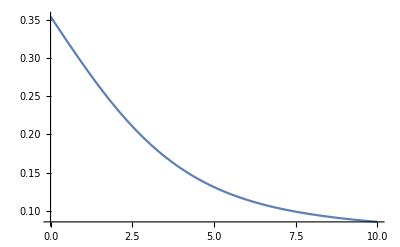

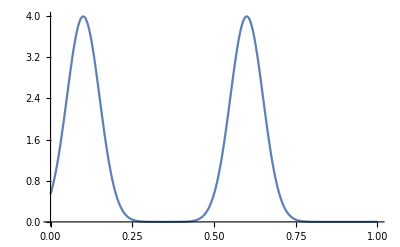

anim.gif

```mathematica
(*Virginia iGEM 2018 Bimodality and Growth Below is Mathematica code with integral equations describing the growth of a population that is bimodally activated.Each mode of activation is distributed normally.Activation (x) ranges from 0 to 1,and the rate of growth is maximum when x=0,and nonexistent when x=1. The former represents bacteria in the growth phase,the latter those bacteria who experience unsustainable metabolic strain from activation.

Variables and Constants x=activation t=time k=% of initial population in A 1-k=% of initial population in B ma=mean activation of A sa=std dev of activation in A mb=mean activation of B sb=std dev of activation in B Functions P:initial distribution of A and B:area=inital population=1 G:growth of P over time:area=population relative to initial M:normalization function for growth:for visualizing relative distribution nG:normalized growth of P over time:relative distribution:area=1 S:total rate of GFP production in the colony at time t A:average rate of GFP production among cells at time t T:total,integral GFP output at time t-------------------------------*)P[x_,k_,ma_,sa_,mb_,sb_]:=(1/Sqrt[2*Pi])*((k/sa)*E^(-(x-ma)^2/(2*sa^2))+((1-k)/sb)*E^(-(x-mb)^2/(2*sb^2)))
M[t_,k_,ma_,sa_,mb_,sb_]:=NIntegrate[E^((1-x1)*t)*P[x1,k,ma,sa,mb,sb],{x1,0,1}]
G[x_,t_,k_,ma_,sa_,mb_,sb_]:=P[x,k,ma,sa,mb,sb]*E^((1-x)*t)
nG[x_,t_,k_,ma_,sa_,mb_,sb_]:=P[x,k,ma,sa,mb,sb]*E^((1-x)*t)/M[t,k,ma,sa,mb,sb]
A[t_,k_,ma_,sa_,mb_,sb_]:=NIntegrate[x2*nG[x2,t,k,ma,sa,mb,sb],{x2,0,1}]
S[t_,k_,ma_,sa_,mb_,sb_]:=NIntegrate[x2*G[x2,t,k,ma,sa,mb,sb],{x2,0,1}]
Ts[tf_,k_,ma_,sa_,mb_,sb_]:=NIntegrate[x2*G[x2,t2,k,ma,sa,mb,sb],{t2,0,tf},{x2,0,1}]
Ta[tf_,k_,ma_,sa_,mb_,sb_]:=NIntegrate[x2*P[x2,k,ma,sa,mb,sb]*E^((1-x2)*t2)/(E^((1-x1)*t2)*P[x1,k,ma,sa,mb,sb]),{x1,0,1},{t2,0,tf},{x2,0,1}]


K=0.5;
MA=0.1;
SA=0.05;
MB=0.6;
SB=0.05;

Plot[A[t1,K,MA,SA,MB,SB],{t1,0,10},PlotRange->{{0,10},Full}]
Plot[P[x1,K,MA,SA,MB,SB],{x1,0,1},PlotRange->{{0,1},Full}]

Animate[DiscretePlot[nG[x1,t1,K,MA,SA,MB,SB],{x1,0,1,0.01},PlotRange->{{0,1},{0,10}},Joined->True],{t1,0,10,0.1},AnimationRunning->False,AnimationRate->1,DefaultDuration->5]

gif=Table[DiscretePlot[nG[x1,t1,K,MA,SA,MB,SB],{x1,0,1,0.01},PlotRange->{{0,1},{0,10}},Joined->True],{t1,0,10,1}];

Export["anim.gif",gif,"DisplayDurations"->1]
```